20+44 x+13 x^2-24 x^3-10 x^4+4 x^5+x^6

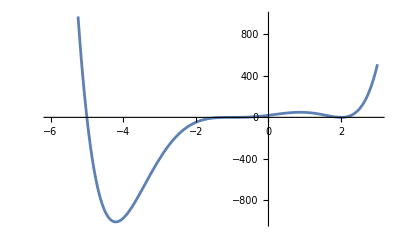

Графически: x = -1; x = 2; x=-5

Solve: {{x→-5},{x→-1},{x→-1},{x→-1},{x→2},{x→2}}

NSolve: {{x→-5.},{x→-1.},{x→-1.},{x→-1.},{x→2.},{x→2.}}

Roots: x==-5||x==-1||x==-1||x==-1||x==2||x==2

FindRoot: {x→-5.}

(-2+x)^2 (1+x)^3 (5+x)

```mathematica
f[x_]=x^6+4x^5-10x^4-24x^3+13x^2+44x+20

Plot[f[x], {x, -6, 3}]

Print["Графически: x = -1; x = 2; x=-5"]
Print["Solve: ",Solve[f[x]==0, x]]
Print["NSolve: ", NSolve[f[x]==0, x]]
Print["Roots: ",Roots[f[x]==0, x]]
Print["FindRoot: ",FindRoot[f[x]==0, {x,-5}]]
Factor[f[x]]
```